```mathematica
Clear["Global`*"]
```

### Table 2

```mathematica
rawRanLengths={-0.6787219230526584,0.7621351560306098,-0.9171786598573886,0.35209781545952484,-0.5674278557198684,0.9214761206455304,0.8244677200486106,-0.6968483735543598};
```

### Eqs. (4)

```mathematica
Module[{Ν=8,m=3,ℓ=1},
lengthsAlt[Δ_]:=Table[ℓ+((-1)^n+Mod[Ν,2]/Ν)Δ,
{n,Ν}];
lengthsRan[Δ_]:=Table[ℓ+(rawRanLengths[[n]]-Mean@rawRanLengths)Δ,
{n,Ν}];
lengthsLin[Δ_]:=Table[ℓ+((2n-Ν-1)/(Ν-1))Δ,
{n,Ν}];
lengthsImp[Δ_]:=Table[ℓ+((KroneckerDelta[m,n]Ν-1)/(Ν-1))Δ,
{n,Ν}];
]
```

### Eq . (8)

```mathematica
popStandDev[lengths_]:=√(Mean[lengths^2]-Mean[lengths]^2)
```

### Eqs. (9)

```mathematica
$Assumptions={Δ>=0};
popStandDev/@{lengthsAlt[Δ],lengthsRan[Δ],lengthsLin[Δ],lengthsImp[Δ]}//FullSimplify//Chop
```

{Δ,0.736812 √(Δ^2),√(3/7) Δ,Δ/(√7)}

### Eq. (10)

```mathematica
$Assumptions={0<=ℓ<=2};
eq10sub=Solve[
((ℓ-1)^2+σ^2==Δ^2/.Δ->1)&&(σ>=0),σ
]
```

{{σ→√(2 ℓ-ℓ^2)}}

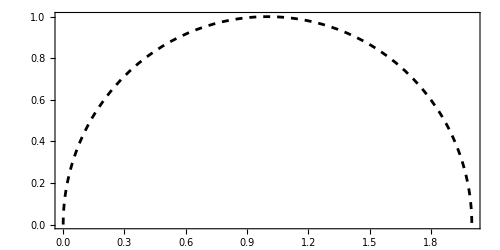

```mathematica
Plot[σ/.eq10sub,{ℓ,0,2}
,LabelStyle->{FontFamily->"Times New Roman",FontSize->18}
,ImageSize->500
,AspectRatio->0.5
,Axes->False,Frame->True,FrameStyle->Black
,PlotRangePadding->{0,0.001}
,PlotStyle->Directive[Black,Dashed]
,FrameLabel->(Style[#,FontSize->25]&/@{"",Rotate[ "",-90Degree]})
]
```